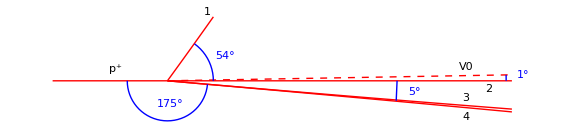

```mathematica
CurvedPath[r_, α_, q_] := Circle[{q*r*Tan[α*Pi/180]/Sqrt[1+Tan[α*Pi/180]^2],-q*r/Sqrt[1+Tan[α*Pi/180]^2]},r]
ParticlePath[x_,r_,α_,q_]:=-b/Abs[b] * Sqrt[r^2-(x-a)^2]+b/.{a->q*r*Tan[α*Pi/180]/Sqrt[1+Tan[α*Pi/180]^2],b->-q*r/Sqrt[1+Tan[α*Pi/180]^2]}
r1 = {47, 3};
r2 = Infinity;
r3 = {300, 20};
r4 = {490, 20};
Show[
Graphics[{Red,Thick, Line[{{-1,0},{0,0}}]}],
Graphics[{Red,Dashed,Line[{{0,0},{3*Cos[Pi/180],3*Sin[Pi/180]}}]}],
Plot[ParticlePath[x,r1[[1]],54,-1],{x,0,0.4},PlotStyle->{Red,Thick}],
Plot[ParticlePath[x, r3[[1]],-5,-1],{x,0,3},PlotStyle->{Red,Thick}],
Plot[ParticlePath[x,r4[[1]],-5,1],{x,0,3},PlotStyle->{Red,Thick}],
Graphics[{Red,Thick, Line[{{0,0},{3,0}}]}],
Graphics[Text[Style["p^+",Medium],{-0.45, 0.1}]],
Graphics[Text[Style["1",Medium],{0.35,0.6}]],
Graphics[Text[Style["2",Medium],{2.8,-0.07}]],
Graphics[Text[Style["3",Medium],{2.6,-0.15}]],
Graphics[Text[Style["4",Medium],{2.6, -0.32}]],
Graphics[Text[Style["V0",Medium], {2.6, 0.12}]],
Graphics[{Blue,Circle[{0,0},0.4,{0,54 *Pi/180}]}],
Graphics[{Blue,Text[Style["54°",Medium],{0.5, 0.22}]}],
Graphics[{Blue,Circle[{0,0},2,{0,-5 *Pi/180}]}],
Graphics[{Blue,Text[Style["5°",Medium],{2.15, -0.1}]}],
Graphics[{Blue,Circle[{0,0},0.35,{-Pi,-5*Pi/180}]}],
Graphics[{Blue,Text[Style["175°",Medium],{0.02,-0.2}]}],
Graphics[{Blue,Circle[{0,0},2.95,{0,Pi/180}]}],
Graphics[{Blue,Text[Style["1°",Medium],{3.1, 0.05}]}],
Axes->{False,False},
ImageSize->Large
]
```

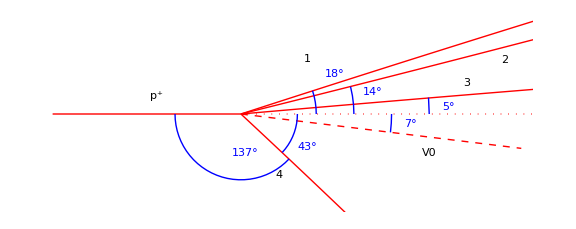

```mathematica
R1 = {125,5};
R2 = {160,5};
R3 = {245,5};
R4 = {56,3};
R5 = {280, 10};
R6 = {830, 30};
Q1 = 1;
Q2 = -1;
Q3 = 1;
Q4 = 1;
Angle1 = {18,1};
Angle2 = {14,1};
Angle3 = {5,1};
Angle4 = {-43,1};
AngleV0 = {-7,1};
Show[
Graphics[{Red,Thick, Line[{{-1,0},{0,0}}]}],
Graphics[{Red,Dashed,Line[{{0,0},{1.5*Cos[-7*Pi/180],1.5*Sin[-7*Pi/180]}}]}],
Plot[ParticlePath[x,R1[[1]],Angle1[[1]],Q1],{x,0,2},PlotStyle->{Red,Thick}],
Plot[ParticlePath[x,R2[[1]],Angle2[[1]],Q2],{x,0,2},PlotStyle->{Red,Thick}],
Plot[ParticlePath[x,R3[[1]],Angle3[[1]],Q3],{x,0,2},PlotStyle->{Red,Thick}],
Plot[ParticlePath[x,R4[[1]],Angle4[[1]],Q4],{x,0,2},PlotStyle->{Red,Thick}],

Graphics[{Blue,Circle[{0,0},0.4,{0,Angle1 [[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["18°",Medium],{0.5, 0.22}]}],
Graphics[{Blue,Circle[{0,0},0.6,{0,Angle2[[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["14°",Medium],{0.7, 0.12}]}],
Graphics[{Blue,Circle[{0,0},0.35,{-Pi,-43Pi/180}]}],
Graphics[{Blue,Text[Style["137°",Medium],{0.02,-0.2}]}],
Graphics[{Blue,Circle[{0,0},1.0,{0,Angle3[[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["5°",Medium],{1.1, 0.045}]}],
Graphics[{Blue,Circle[{0,0},0.8,{0,AngleV0[[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["7°",Medium],{0.9, -0.047}]}],
Graphics[{Blue,Circle[{0,0},0.3,{0,Angle4[[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["43°",Medium],{0.35, -0.17}]}],

Graphics[{Red, Dotted,Thin, Line[{{0,0},{2,0}}]}],
Graphics[Text[Style["p^+",Medium],{-0.45, 0.1}]],
Graphics[Text[Style["1",Medium],{0.35,0.3}]],
Graphics[Text[Style["2",Medium],{1.4,0.29}]],
Graphics[Text[Style["3",Medium],{1.2,0.17}]],
Graphics[Text[Style["4",Medium],{0.2, -0.32}]],
Graphics[Text[Style["V0",Medium], {1.0, -0.2}]],
(*Graphics[Text[Style["2881",Large],{-0.5, 0.3}]],*)
Axes->{False,False},
PlotRange->{{-1,1.5},{-0.5,0.5}},
ImageSize -> Large
]
```

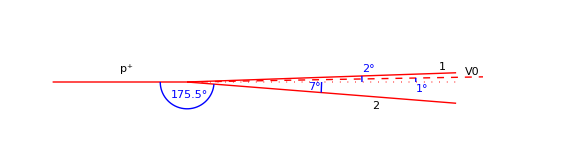

```mathematica
ParticlePath[x_,r_,α_,q_]:=-b/Abs[b] * Sqrt[r^2-(x-a)^2]+b/.{a->q*r*Tan[α*Pi/180]/Sqrt[1+Tan[α*Pi/180]^2],b->-q*r/Sqrt[1+Tan[α*Pi/180]^2]}
R1 = {2000, 200};
R2 = {1700, 100};
Q1 = 1;
Q2 = 1;
Angle1 = {2, 0.3};
AngleV0 = {1, Sqrt[0.1^2 + 0.3^2]};
Angle2 = {-4.5, 0.3};
Show[
Graphics[{Red,Thick, Line[{{-1,0},{0,0}}]}],
Graphics[{Red,Dashed,Line[{{0,0},{2.2*Cos[AngleV0[[1]]*Pi/180],2.2Sin[AngleV0[[1]]*Pi/180]}}]}],
Plot[ParticlePath[x,R1[[1]],Angle1[[1]],Q1],{x,0,2},PlotStyle->{Red,Thick}],
Plot[ParticlePath[x,R2[[1]],Angle2[[1]],Q2],{x,0,2},PlotStyle->{Red,Thick}],

Graphics[{Blue,Circle[{0,0},1.3,{0,Angle1 [[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["2°",Medium],{1.35, 0.1}]}],
Graphics[{Blue,Circle[{0,0},1,{0,Angle2[[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["1°",Medium],{1.75, -0.05}]}],
Graphics[{Blue,Circle[{0,0},0.2,{-Pi,Angle2[[1]]Pi/180}]}],
Graphics[{Blue,Text[Style["175.5°",Medium],{0.02,-0.1}]}],
Graphics[{Blue,Circle[{0,0},1.7,{0,AngleV0[[1]]*Pi/180}]}],
Graphics[{Blue,Text[Style["7°",Medium],{0.95, -0.035}]}],

Graphics[{Red, Dotted,Thin, Line[{{0,0},{2,0}}]}],
Graphics[Text[Style["p^+",Medium],{-0.45, 0.1}]],
Graphics[Text[Style["1",Medium],{1.9,0.11}]],
Graphics[Text[Style["2",Medium],{1.4,-0.18}]],
Graphics[Text[Style["V0",Medium], {2.12, 0.075}]],
Axes->{False,False},
PlotRange->{{-1,2.5},{-0.5,0.5}},
ImageSize -> Large
]
```

```mathematica
V={0.852374744,0.00264111};
p[r_,Δr_] := {0.3*17.4*V[[1]]*r, 0.3*17.4*Sqrt[r^2 *V[[2]]^2 + Δr^2*V[[1]]^2]}
(*2881 analysis*)
R1 = {125,5};
R2 = {160,5};
R3 = {245,5};
R4 = {56,3};
R5 = {280, 10};
R6 = {830, 30};
Q1 = 1;
Q2 = -1;
Q3 = 1;
Q4 = 1;
Angle1 = {18,1};
Angle2 = {14,1};
Angle3 = {5,1};
Angle4 = {-43,1};
AngleV0 = {-7,1};
P1 = p[R1[[1]], R1[[2]]];
P2 = p[R2[[1]], R2[[2]]];
P3 = p[R3[[1]], R3[[2]]];
P4 = p[R4[[1]], R4[[2]]];
P5 = p[R5[[1]], R5[[2]]]
P6 = p[R6[[1]], R6[[2]]]
TwoDMomentum[P_, θ_] := {P[[1]]*Cos[θ[[1]]*Pi/180], P[[1]]*Sin[θ[[1]]*Pi/180], Sqrt[P[[1]]^2*Sin[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Cos[Pi*θ[[1]]/180]^2],Sqrt[P[[1]]^2*Cos[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Sin[θ[[1]]*Pi/180]^2]} 
(*Sums two momenta, adding errors as independent variables*)
sumTwo[pa_, pb_] := {pa[[1]] + pb[[1]], pa[[2]] + pb[[2]], Sqrt[pa[[3]]^2 + pb[[3]]^2], Sqrt[pa[[4]]^2 + pb[[4]]^2]}
(*Format: {px, py, px error, py error}*)

(*Gives magnitude of momentum; input form: {px, py, error px, error py}*)
magnitude[mom_] := {Sqrt[mom[[1]]^2 + mom[[2]]^2],(1/Sqrt[mom[[1]]^2 + mom[[2]]^2])*Sqrt[mom[[1]]^2*mom[[3]]^2 + mom[[2]]^2*mom[[4]]^2] }
p1 = TwoDMomentum[P1, Angle1]
p2 = TwoDMomentum[P2, Angle2]
p3 = TwoDMomentum[P3, Angle3]
p4 = TwoDMomentum[P4, Angle4]
p5 = TwoDMomentum[P5, AngleV0] (*4902.02, -601.892,140.412, 69.6758*)
p6 = TwoDMomentum[P6, AngleV0]
p7 = TwoDMomentum[P5, {0.1, 0.01}]
p8 = TwoDMomentum[P6, {-0.1, 0.01}]
pV0 = sumTwo[p5, p6]
pV02 = sumTwo[p7, p8]
p11 = sumTwo[p1, p2];
p12 = sumTwo[p11, p3];
p13 = sumTwo[p12, p4]
```

{1245.83,44.6611}

{3693.,133.971}

{528.953,171.867,21.4325,11.5228}

{690.757,172.225,21.8993,13.2135}

{1085.95,95.0087,22.4776,19.0547}

{182.229,-169.931,10.2184,9.6574}

{1236.54,-151.829,44.4073,22.2575}

{3665.47,-450.063,133.205,66.0251}

{1245.83,2.17438,44.661,0.230988}

{3692.99,-6.4455,133.971,0.685651}

{4902.02,-601.892,140.412,69.6758}

{4938.82,-4.27111,141.219,0.723514}

{2487.89,269.17,39.3521,27.6354}

```mathematica
(*5.1 Testing association*)
r1 = {85, 5};
r2 = {17.5, 0.5};
P1 = p[r1[[1]], r1[[2]]]
P2 = p[r2[[1]], r2[[2]]] 
α1 = {11, 0.2};
α2  = {-78, 0.2};
p1 = TwoDMomentum[P1, α1]
p2 = TwoDMomentum[P2, α2]
p12 = sumTwo[p1,p2]
magnitude[p12]
```

{378.199,22.2778}

{77.8644,2.23774}

{371.25,72.1637,21.87,4.44396}

{16.1889,-76.1629,0.535855,2.18957}

{387.439,-3.9992,21.8765,4.95409}

{387.46,21.8754}

```mathematica
(*5.3 Testing of the Primary Reaction*)
r3 ={4000,500};
r4 = {910,50};
P0 = magnitude[p12];
P3 = p[r3[[1]], r3[[2]]]
P4 = p[r4[[1]], r4[[2]]]
α0 = {42, 0.2};
α3 = {-0.3, 0.1};
α4 = {-2.7, 0.1};
p0 = TwoDMomentum[P0, α0]
p3 = TwoDMomentum[P3, α3]
p4 =TwoDMomentum[P4, α4]
psum = sumTwo[sumTwo[p0, p3], p4]
(*Energy function: takes m and {p, Δp} as variables*)
Energy[m_, p_] :={ Sqrt[m^2 + p[[1]]^2], p[[1]]*p[[2]]/Sqrt[m^2 + p[[1]]^2]}
addEnergy[E1_, E2_]:= {E1[[1]]+E2[[1]], Sqrt[E1[[2]]^2 + E2[[2]]^2]}
E3 = Energy[938, magnitude[p3]]
E4 = Energy[493.677, magnitude[p4]]
EΛ = Energy[1115.683, magnitude[p0]]
EpKΛ = addEnergy[addEnergy[E4, EΛ], E3]
```

{17797.6,2225.38}

{4048.95,222.823}

{287.939,259.261,16.2818,14.672}

{17797.3,-93.1875,2225.35,33.1758}

{4044.46,-190.732,222.576,12.6492}

{22129.7,-24.6581,2236.51,38.4175}

{17822.3,2222.24}

{4078.94,220.695}

{1181.05,5.11177}

{23082.3,2233.17}

```mathematica
{4044.455667611072,-190.73168757557923,222.57616400688147,12.649223914754899}
```

{22129.7,-24.6581,2236.51,38.4175}

{17822.3,2222.24}

{4078.94,220.695}

{1181.05,5.11177}

{23082.3,2233.17}

```mathematica
(*Our p->x,y,V0 event*)
```

```mathematica
(*1. Assignment of V0 vertex to primary vertex: automatic, as the angle between the two V0 products is 0.1 +- 0.1, practically 0*)
V={0.852374744,0.00264111};
p[r_,Δr_] := {0.3*17.4*V[[1]]*r, 0.3*17.4*Sqrt[r^2 *V[[2]]^2 + Δr^2*V[[1]]^2]}
TwoDMomentum[P_, θ_] := {P[[1]]*Cos[θ[[1]]*Pi/180], P[[1]]*Sin[θ[[1]]*Pi/180], Sqrt[P[[1]]^2*Sin[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Cos[Pi*θ[[1]]/180]^2],Sqrt[P[[1]]^2*Cos[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Sin[θ[[1]]*Pi/180]^2]} 
sumTwo[pa_, pb_] := {pa[[1]] + pb[[1]], pa[[2]] + pb[[2]], Sqrt[pa[[3]]^2 + pb[[3]]^2], Sqrt[pa[[4]]^2 + pb[[4]]^2]}
magnitude[mom_] := {Sqrt[mom[[1]]^2 + mom[[2]]^2],(1/Sqrt[mom[[1]]^2 + mom[[2]]^2])*Sqrt[mom[[1]]^2*mom[[3]]^2 + mom[[2]]^2*mom[[4]]^2] }
RV01 = {56,2};
RV02 = {750, 50};
PV01 = p[RV01[[1]], RV01[[2]]];
PV02 = p[RV02[[1]], RV02[[2]]];
αV01 ={0, 0.05};
αV02 = {0, 0.05};
pV01 = TwoDMomentum[PV01, αV01]
pV02 = TwoDMomentum[PV02, αV02];
pV0 = sumTwo[pV01, pV02];
PV0 = magnitude[pV0]

R1 = {2000, 200};
R2 = {1700, 100};
Angle1 = {2, 0.3};
Angle2 = {-4.5, 0.3};
AngleV0 = {1, 0.3};
P1 = p[R1[[1]], R1[[2]]];
P2 = p[R2[[1]], R2[[2]]];
p1 = TwoDMomentum[P1, Angle1];
p2 = TwoDMomentum[P2, Angle2];
pV0 = TwoDMomentum[PV0, AngleV0]
pSum = sumTwo[sumTwo[p1, p2], pV0]
(*The results say there is more missing momentum than that of the incoming proton, thus there should be another particle (at least)*)
(*Trying different pairs for V0 decay*)
mV0[m1_, m2_] := {Sqrt[(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 - PV0[[1]]^2], (1/Sqrt[(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 - PV0[[1]]^2])*Sqrt[((PV01[[1]]*PV01[[2]]/Sqrt[m1^2 + PV01[[1]]^2])^2 + (PV02[[1]]*PV02[[2]]/Sqrt[m2^2 + PV02[[1]]^2])^2)*(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 + PV0[[1]]^2*PV0[[2]]^2]}
(*Testing with Seul data to confirm
PV01 = {370, 22};
PV02 = {76, 3};
PV0 = {379, 22};
Results in {1104.3,11.5}*)
(*pion-proton:*)
m2 = 938.3;
m1 = 139.6;
mK = 493.7;
mp = 938.3;
(*Huge error, similar to german E212 Tabelle 5*)
mV0[m1, m2]
(*pion-pion, even larger error*)
mV0[m1, m1]
(*Thus an analysis is not decisive (same thing happens for muons, m = 105.7 MeV)*)
pp ={23877-sumTwo[p1, p2][[1]], -sumTwo[p1, p2][[2]], sumTwo[p1, p2][[3]], sumTwo[p1, p2][[4]]}
Epp = 23895 + 938
Energy[m_, p_] := {N[Sqrt[m^2 + p[[1]]^2 + p[[2]]^2]], N[(1/Sqrt[m^2 + p[[1]]^2 + p[[2]]^2])*Sqrt[p[[1]]^2*p[[3]]^2 + p[[2]]^2*p[[4]]^2]] }
AddEnergies[En1_, En2_, En3_] := {En1[[1]] + En2[[1]] + En3[[1]], Sqrt[En1[[2]]^2 + En2[[2]]^2 + En3[[2]]^2]}
(*Σ0 particle has mass 1192.6 MeV*)
Energy[mp, p1]
Energy[mK,p2]
Energy[1192.6, pp]
mPi0 = 134.9766;
AddEnergies4[En1_, En2_, En3_, En4_] := {En1[[1]] + En2[[1]] + En3[[1]] + En4[[1]], Sqrt[En1[[2]]^2 + En2[[2]]^2 + En3[[2]]^2+En4[[2]]^2]}
AddEnergies[Energy[1192.6, pp],Energy[mp, p1],Energy[mK,p2]]
AddEnergies[Energy[1192.6, pp],Energy[mK, p1],Energy[mp,p2]]
AddEnergies[Energy[1192.6, pp],Energy[mK, p1],Energy[mp,p2]]
AddEnergies4[Energy[1115.6, pV0], Energy[mp, p1], Energy[mK, p2], Energy[mPi0, sumTwo[pp, -pV0]]]
AddEnergies4[Energy[1192.6, pV0], Energy[mp, p1], Energy[mK, p2], Energy[mPi0, sumTwo[pp, -pV0]]]
```

{249.166,0.,8.93222,0.217439}

{3586.21,222.889}

{3585.67,62.5881,222.855,19.1733}

{20019.7,-220.311,1019.14,79.2612}

{1103.19,1028.3}

{532.785,2132.25}

{7442.97,282.899,994.48,76.9072}

24833

{8948.12,884.323}

{7580.07,441.904}

{7543.22,981.268}

{24071.4,1392.91}

{24077.6,1394.39}

{24077.6,1394.39}

{24149.9,1434.09}

{24173.5,1433.89}

```mathematica
(*2881*)
V={0.852374744,0.00264111};
p[r_,Δr_] := {0.3*17.4*V[[1]]*r, 0.3*17.4*Sqrt[r^2 *V[[2]]^2 + Δr^2*V[[1]]^2]}
TwoDMomentum[P_, θ_] := {P[[1]]*Cos[θ[[1]]*Pi/180], P[[1]]*Sin[θ[[1]]*Pi/180], Sqrt[P[[1]]^2*Sin[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Cos[Pi*θ[[1]]/180]^2],Sqrt[P[[1]]^2*Cos[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Sin[θ[[1]]*Pi/180]^2]} 
sumTwo[pa_, pb_] := {pa[[1]] + pb[[1]], pa[[2]] + pb[[2]], Sqrt[pa[[3]]^2 + pb[[3]]^2], Sqrt[pa[[4]]^2 + pb[[4]]^2]}
magnitude[mom_] := {Sqrt[mom[[1]]^2 + mom[[2]]^2],(1/Sqrt[mom[[1]]^2 + mom[[2]]^2])*Sqrt[mom[[1]]^2*mom[[3]]^2 + mom[[2]]^2*mom[[4]]^2] }
mV0[m1_, m2_] := {Sqrt[(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 - PV0[[1]]^2], (1/Sqrt[(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 - PV0[[1]]^2])*Sqrt[((PV01[[1]]* PV01[[2]]/Sqrt[m1^2 +PV01[[1]]^2])^2 + (PV02[[1]]* PV02[[2]]/Sqrt[m2^2 + PV02[[1]]^2])^2)*(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 + PV0[[1]]^2*PV0[[2]]^2]} 
R1 = {125, 5};
R2 = {160, 5};
R3 = {245, 5};
R4 = {56, 3};
R5 = {280, 10};
R6 = {830, 30};
Angle1 = {18, 1};
Angle2 = {14, 1};
Angle3 = {5, 1};
Angle4 = {-43, 1};
AngleV0 = {-7, 1};
Angle5 = {0.05, 0.05};
Angle6 = {-0.05, 0.05};
P1 = p[R1[[1]], R1[[2]]];
P2 = p[R2[[1]], R2[[2]]];
P3 = p[R3[[1]], R3[[2]]];
P4 = p[R4[[1]], R4[[2]]];
PV01 = p[R5[[1]], R5[[2]]]
PV02 = p[R6[[1]], R6[[2]]]
p5 = TwoDMomentum[P5, Angle5];
p6 = TwoDMomentum[P6, Angle6];
PV0 = magnitude[sumTwo[p5, p6]]
p1 = TwoDMomentum[P1, Angle1]
p2 = TwoDMomentum[P2, Angle2]
p3 = TwoDMomentum[P3, Angle3]
p4 = TwoDMomentum[P4, Angle4]
pSum = sumTwo[sumTwo[sumTwo[p1, p2],p3], p4]
m2 = 938.3;
m1 = 139.6;
mV0[m1, m2];
mV0[m1, m1];
(* Check for energy conversation in case of short lifetime neutral particle + 2 positively charged particles*)
pp ={23877-pSum[[1]], -pSum[[2]], pSum[[3]], pSum[[4]]}
pV0 = TwoDMomentum[PV0, AngleV0]
```

{1245.83,44.6611}

{3693.,133.971}

{4938.83,141.22}

{528.953,171.867,21.4325,11.5228}

{690.757,172.225,21.8993,13.2135}

{1085.95,95.0087,22.4776,19.0547}

{182.229,-169.931,10.2184,9.6574}

{2487.89,269.17,39.3521,27.6354}

{21389.1,-269.17,39.3521,27.6354}

{4902.02,-601.892,140.56,87.2701}

```mathematica
V={0.852374744,0.00264111};
p[r_,Δr_] := {0.3*17.4*V[[1]]*r, 0.3*17.4*Sqrt[r^2 *V[[2]]^2 + Δr^2*V[[1]]^2]}
TwoDMomentum[P_, θ_] := {P[[1]]*Cos[θ[[1]]*Pi/180], P[[1]]*Sin[θ[[1]]*Pi/180], Sqrt[P[[1]]^2*Sin[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Cos[Pi*θ[[1]]/180]^2],Sqrt[P[[1]]^2*Cos[θ[[1]]*Pi/180]^2*θ[[2]]^2*(Pi/180)^2+P[[2]]^2*Sin[θ[[1]]*Pi/180]^2]} 
sumTwo[pa_, pb_] := {pa[[1]] + pb[[1]], pa[[2]] + pb[[2]], Sqrt[pa[[3]]^2 + pb[[3]]^2], Sqrt[pa[[4]]^2 + pb[[4]]^2]}
magnitude[mom_] := {Sqrt[mom[[1]]^2 + mom[[2]]^2],(1/Sqrt[mom[[1]]^2 + mom[[2]]^2])*Sqrt[mom[[1]]^2*mom[[3]]^2 + mom[[2]]^2*mom[[4]]^2] }
mV0[m1_, m2_] := {Sqrt[(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 - PV0[[1]]^2], (1/Sqrt[(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 - PV0[[1]]^2])*Sqrt[((PV01[[1]]* PV01[[2]]/Sqrt[m1^2 +PV01[[1]]^2])^2 + (PV02[[1]]* PV02[[2]]/Sqrt[m2^2 + PV02[[1]]^2])^2)*(Sqrt[m1^2 + PV01[[1]]^2]+Sqrt[m2^2 + PV02[[1]]^2])^2 + PV0[[1]]^2*PV0[[2]]^2]} 
R1 = {47, 3};
R2 = {3300, 500};
R3 = {300, 20};
R4 = {490, 20};
Angle1 = {54, 1};
Angle2 = {0, 0.5};
Angle3 =  {-5, 0.5};
Angle4 = {-5, 0.5};
Angle5 = {0.1, 0.1};
Angle6 = {0.1, 0.1};
AngleV0 = {1, 0.5};
R5 = {320, 20};
R6 = {62, 3};
P1 = p[R1[[1]], R1[[2]]];
P2 = p[R2[[1]], R2[[2]]];
P3 = p[R3[[1]], R3[[2]]];
P4 = p[R4[[1]], R4[[2]]];
PV01 = p[R5[[1]], R5[[2]]];
PV02 = p[R6[[1]], R6[[2]]];
p5 = TwoDMomentum[PV01, Angle5];
p6 = TwoDMomentum[PV02, Angle6];
PV0 = magnitude[sumTwo[p5, p6]];
p1 = TwoDMomentum[P1, Angle1];
p2 = TwoDMomentum[P2, Angle2];
p3 = TwoDMomentum[P3, Angle3];
p4 = TwoDMomentum[P4, Angle4];
pV0 = TwoDMomentum[PV0, AngleV0];
pSum = sumTwo[sumTwo[sumTwo[sumTwo[p1, p2],p3], p4],pV0];
m2 = 938.3;
m1 = 139.6;
mμ = 105.7;
mπ = m1;
"Pi+ Pi-"
mV0[m1, m1]
"P pi-"
mV0[m1, m2]
mV0[m2, m1];
mV0[mμ, m1]
mV0[m1, mμ]
(* Check for energy conversation in case of short lifetime neutral particle + 2 positively charged particles*)
pp ={23877-pSum[[1]], -pSum[[2]], pSum[[3]], pSum[[4]]};
mK = 493.7;
mp = 938.3;
mΛ = 1115.7;
mΣ = 1189.37;
mΞ = 1314.9;
Q1 = 1;
Q2 = 1;
Q3 = -1;
Q4 = 1;
mPi0 = 134.9766;
AddEnergies[E1_, E2_, E3_, E4_, E5_] := {E1[[1]] + E2[[1]] + E3[[1]] + E4[[1]] + E5[[1]], Sqrt[E1[[2]]^2 + E2[[2]]^2 + E3[[2]]^2 + E4[[2]]^2 + E5[[2]]^2]}
AddEnergiesExtra[E1_, E2_, E3_, E4_, E5_, E6_] := {E1[[1]] + E2[[1]] + E3[[1]] + E4[[1]] + E5[[1]] + E6[[1]], Sqrt[E1[[2]]^2 + E2[[2]]^2 + E3[[2]]^2 + E4[[2]]^2 + E5[[2]]^2 + E6[[2]]^2]}
AddEnergiesExtra[Energy[mp, p2], Energy[mp, p1], Energy[mK, pV0], Energy[mK, p4], Energy[mπ, p3], Energy[mPi0,{0,0,0,0}]]
AddEnergiesExtra[Energy[mp, p2], Energy[mp, p1], Energy[mK, pV0], Energy[mK,p4], Energy[mπ, p3], Energy[mPi0, pp-pV0]]
Epp = 23895 + 938
sumTwo[pp, -pV0]
```

Pi+ Pi-

{371.557,587.685}

P pi-

{1706.66,154.079}

{357.687,610.575}

{300.641,723.708}

{21156.7,2225.74}

{23197.9,3084.15}

24833

{2170.61,77.8449,2232.36,132.662}

```mathematica
(*One can try a sigma0 again*)
```